```mathematica
n=9; (* Number of eigenstates *)
L=3; (* Size of the box *)
δ[x_]:={x,-L,L};
```

```mathematica
V[x_]:=Piecewise[{{0,Abs[x]<L},{10^6,True}}];
```

```mathematica
{{μ,λ},{ϕ,ψ}}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+# u[x],DirichletCondition[u[x]==0,True]},u[x],δ[x],n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->10^-3}}}}]&/@{V[x],x^2}//Transpose;
```

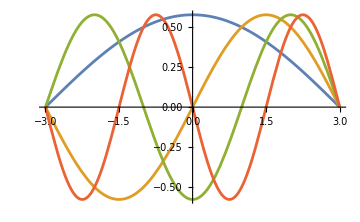
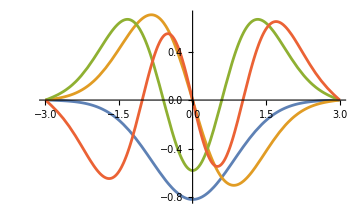

```mathematica
Plot[Take[#,4]//Evaluate,δ[x],PlotRange->All,ImageSize->Medium]&/@{ϕ,ψ}
```

```mathematica
Sort[#]&/@{μ,λ}//Column
```

{0.137078,0.548311,1.2337,2.19325,3.42695,4.9348,6.71681,8.77298,11.1033}
{0.707123,2.12169,3.53943,4.97382,6.46302,8.07278,9.87433,11.918,14.2281}

```mathematica
β=Abs[#]^2&/@ψ;
```

```mathematica
NIntegrate[#,δ[x],PrecisionGoal->4]&/@β
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
If[OddQ[n],
ν=2&/@Range[1,n-1];
AppendTo[ν,1],
ν=2&/@Range[1,hntyyttyyuyn]
]
Length@ν
```

{2,2,2,2,2,2,2,2,1}

9

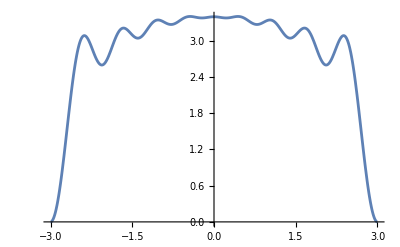

```mathematica
ρ[y_]:=ν.β/.{x->y};
Plot[ρ[x],δ[x],PlotRange->All]
```

```mathematica
Subscript[E, LDA]=-3/4(3/π)^(1/3)NIntegrate[ρ[x]^(4/3),δ[x],PrecisionGoal->4]
```

-18.213

```mathematica
Subscript[v, LDA]=-(3/π)^(1/3)ρ[x]^(1/3);
```

```mathematica
ϵ=10^-1//N;
Subscript[E, Ha]=1/2 NIntegrate[(ρ[x]ρ[y])/(√((x-y)^2+ϵ)),δ[x],δ[y],PrecisionGoal->3]
```

139.649

```mathematica
Δ=N@Subdivide[-L,L,10^2];
Subscript[v, Ha,values]=NIntegrate[ρ[y]/(√((#-y)^2+ϵ)),δ[y],PrecisionGoal->3]&/@Δ;
```

```mathematica
Subscript[v, Ha]=Transpose[{Δ,Subscript[v, Ha,values]}]//Interpolation[#,InterpolationOrder->5]&;
```

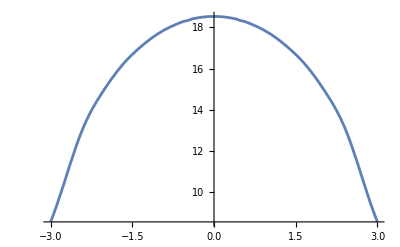

```mathematica
Plot[Subscript[v, Ha][x],δ[x]]
```

```mathematica
(* Actual self-consistent loop for the Kohn-Sham equations *)
{ζ,υ}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+(Subscript[v, Ha][x]+Subscript[v, LDA]+x^2)u[x],DirichletCondition[u[x]==0,True]},u[x],δ[x],n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->10^-3}}}}];
```

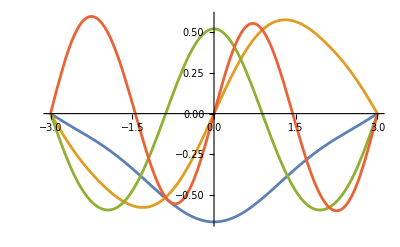

```mathematica
Plot[Take[υ,4]//Evaluate,δ[x],PlotRange->All]
```

```mathematica
Min[ζ]
```

17.3663